```mathematica
Integrate[Cos[θ]^(1-0.001), θ]
```

-1/(√(Sin[θ]^2))0.50025 Cos[θ]^1.999 Hypergeometric2F1[0.5,0.9995,1.9995,Cos[θ]^2] Sin[θ]

```mathematica
Assuming[a>0, Integrate[ξ^(a) / (ξ^2*Sqrt[ξ^2 - 1]), ξ]]
```

(ξ^(-1+a) √(1-ξ^2) Hypergeometric2F1[1/2,1/2 (-1+a),1+1/2 (-1+a),ξ^2])/((-1+a) √(-1+ξ^2))

```mathematica
Simplify[(ξ^(-1+a) √(1-ξ^2) Hypergeometric2F1[1/2,1/2 (-1+a),1+1/2 (-1+a),ξ^2])/((-1+a) √(-1+ξ^2))]
```

(ξ^(-1+a) √(1-ξ^2) Hypergeometric2F1[1/2,1/2 (-1+a),(1+a)/2,ξ^2])/((-1+a) √(-1+ξ^2))

```mathematica
F[ξ_]:=(√(-1+ξ^2))/ξ
G[ξ_,a_]:=(ξ^(-1+a) √(1-ξ^2) Hypergeometric2F1[1/2,1/2 (-1+a),(1+a)/2,ξ^2])/((-1+a) √(-1+ξ^2))
```

```mathematica
Function[ξ,(√(-1+ξ^2))/ξ]
```

Function[ξ,(√(-1+ξ^2))/ξ]

```mathematica
U[ξ_,a_]:= (Re[G[ξ,a]]+ 1 - F[ξ]) * ξ^(-a)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

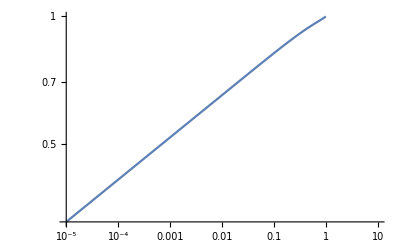

```mathematica
LogLogPlot[U[1/p,0.1], {p,10^-5,10}]
```

```mathematica
FortranForm[Simplify[U[R/p,a]]]
```

(1 - (p*Sqrt(-1 + R**2/p**2))/R + 
     -    Re(((R/p)**(-1 + a)*Sqrt(1 - R**2/p**2)*
     -        Hypergeometric2F1(0.5,(-1 + a)/2.,(1 + a)/2.,
     -         R**2/p**2))/((-1 + a)*Sqrt(-1 + R**2/p**2))))/
     -  (R/p)**a

```mathematica
U[1/0.1,0.01]
```

0.98011